# EDMD Built

## Initialization

### Numerical Variable Definition

```mathematica
eventspercycle = 10; (*Events per sphere per cycle*)
n=20; (*Number of Spheres*)
ipf=.01; (*Initial packing fraction*)
rate=.01; (*Growth rate (relative)*)
mpressure=100; (*max pressure*)
gtime = 0 ;(*global time*)
bratio = .2;
rratio = .4;
size = 1;
nrows=10;
steps=100;
```

### Global Variables

Initializes radii, positions, velocities, nextevents, heap, hash, cellMatrix, cellA, lastupdates in that order.

```mathematica
gtime=0;
radii=rlist[ipf, size, n, bratio, rratio];
positions=createDisks[radii, size];
velocities = velocityInit[size, n];
setInitialEvents[n]
changeBins[nrows]
lastupdates=Table[0, n];
```

```mathematica
nextevents
```

{{0,1,∞},{0,2,∞},{0,3,∞},{0,4,∞},{0,5,∞},{0,6,∞},{0,7,∞},{0,8,∞},{0,9,∞},{0,10,∞}}

```mathematica
nchecks=0;
ntrans = 0;
ncollisions = 0;
```

### Step

```mathematica
Do[
processEvent
, 100];
```

{3.23349,11,24}

{4.55715,11,24}{∞,11,∞}

{4.55715,11,24}

{3.28165,19,21}

A 0.00898282 B 0.013286 C 0.0217313 d -0.00001869

A 0.0308931 B -0.00698107 C 0.0303445 d -0.000888701

{4.13789,19,23}{∞,19,∞}

{4.13789,19,23}

{3.37391,8,22}

{5.3453,8,24}{∞,8,∞}

{5.3453,8,24}

{3.3746,7,21}

A 0.0515205 B 0.0180182 C 0.0236747 d -0.000895079

A 0.00543934 B -5.0266×10^-6 C 0.0159559 d -0.0000867896

{3.75901,7,24}{∞,7,∞}

{3.75901,7,24}

{3.43213,12,23}

A 0.00400461 B -0.00554762 C 0.00749427 d 7.64399×10^-7

{4.43522,12,23}{4.59911,12,14}

{4.43522,12,23}

{3.52787,10,24}

A 0.0340389 B -0.0158273 C 0.0105228 d -0.00010768

{4.14832,10,21}{∞,10,∞}

{4.14832,10,21}

{3.56084,16,23}

A 0.0340389 B -0.0147049 C 0.00951609 d -0.000107684

{4.57338,16,23}{∞,16,∞}

{4.57338,16,23}

{3.75901,7,24}

A 0.00543934 B 0.00208588 C 0.0167571 d -0.0000867968

{4.79944,7,24}{∞,7,∞}

{4.79944,7,24}

{3.82054,9,22}

A 0.00441136 B -0.00687533 C 0.0125155 d -7.94021×10^-6

A 0.00215913 B 0.00245297 C 0.00709282 d -9.29723×10^-6

{4.56046,9,24}{∞,9,∞}

{4.56046,9,24}

{3.85181,1,24}

A 0.0586784 B -0.0121976 C 0.00228476 d 0.000014716

A 0.00726407 B 0.00650862 C 0.00695163 d -8.13497×10^-6

{3.9943,1,22}{3.99431,1,19}

{3.9943,1,22}

{3.86189,5,22}

A 0.00441136 B -0.0066929 C 0.0119545 d -7.94084×10^-6

{5.03547,5,22}{∞,5,∞}

{5.03547,5,22}

{3.90179,20,22}

A 0.00215913 B 0.00262841 C 0.00750599 d -9.29784×10^-6

A 0.00607526 B -0.00241984 C 0.00823791 d -0.0000441918

{4.7262,20,24}{∞,20,∞}

{4.7262,20,24}

{3.9223,4,23}

A 0.0247139 B 0.0310194 C 0.0386657 d 6.62422×10^-6

{4.44365,4,22}{∞,4,∞}

{4.44365,4,22}

{3.94775,3,23}

{4.11511,3,22}{∞,3,∞}

{4.11511,3,22}

{3.9943,1,22}

A 0.0586784 B -0.00383676 C 1.58704×10^-6 d 0.0000146276

A 0.00726407 B 0.00754365 C 0.00895695 d -8.1573×10^-6

{4.78424,1,24}{3.99451,1,19}

{3.99451,1,19}

{3.99451,1,19}

A 0.0586784 B 0.00380422 C 2.19223×10^-9 d 0.000014472

A 0.0179036 B -0.000957289 C 0.00896008 d -0.000159502

{3.99458,1,21}{∞,1,∞}

current, next{3.99451,1,19}{3.99458,1,21}

{3.99451,19,∞}

A 0.0586784 B 0.00380422 C 2.19223×10^-9 d 0.000014472

A 0.0163242 B -0.0082482 C 0.0155834 d -0.000186354

{4.13247,19,23}{∞,19,∞}

{3.99458,1,21}

A 0.0586784 B 0.00380845 C 5.50851×10^-7 d 0.0000144719

A 0.0179036 B -0.000956 C 0.00895995 d -0.000159502

{4.75651,1,24}{∞,1,∞}

{4.75651,1,24}

{4.0656,13,24}

A 0.0103773 B 0.00159682 C 0.0322641 d -0.000332264

A 0.00607526 B -0.00142465 C 0.0076087 d -0.0000441953

{5.31411,13,24}{∞,13,∞}

{5.31411,13,24}

{4.11511,3,22}

{4.94785,3,22}{∞,3,∞}

{4.94785,3,22}

{4.13247,19,23}

A 0.0586784 B 0.0119 C 0.00216816 d 0.0000143862

A 0.0163242 B -0.00599597 C 0.0136196 d -0.000186378

{5.09998,19,23}{∞,19,∞}

{5.09998,19,23}

{4.14832,10,21}

A 0.0340389 B 0.00529212 C 0.00398836 d -0.000107753

A 0.0448834 B -0.0202573 C 0.0127718 d -0.000162883

{5.04973,10,24}{∞,10,∞}

{5.04973,10,24}

{4.21994,17,23}

A 0.00371953 B -0.00729384 C 0.0145233 d -8.19627×10^-7

A 0.0057741 B -0.00645341 C 0.0147575 d -0.0000435651

{5.03321,17,21}{∞,17,∞}

{5.03321,17,21}

{4.42597,15,23}

A 0.0077279 B 0.00434561 C 0.00849528 d -0.0000467663

{5.34577,15,22}{∞,15,∞}

{5.34577,15,22}

{4.43522,12,23}

A 0.00400461 B -0.00153061 C 0.000397602 d 7.50534×10^-7

{5.43832,12,23}{4.6011,12,14}

big mistake

{4.6011,12,14}

{4.44365,4,22}

A 0.00189285 B -0.00730331 C 0.0272382 d 1.78063×10^-6

A 0.0448834 B -0.00700193 C 0.00472448 d -0.000163024

{4.88362,4,23}{7.59705,4,16}

{4.88362,4,23}

{4.55715,11,24}

{5.26152,11,21}{∞,11,∞}

{5.26152,11,21}

{4.6011,14,12}

A 0.00400461 B 0.000859639 C 5.78777×10^-7 d 7.36661×10^-7

A 0.000922647 B -0.00231098 C 0.0106782 d -4.5116×10^-6

{4.43422,14,23}{∞,14,∞}

current, next{4.6011,14,12}{4.43422,14,23}

collision event time error

{4.43422,14,23}

A 0.00400461 B 0.00019135 C -0.000175392 d 7.38993×10^-7

{6.09531,14,23}{∞,14,∞}

{6.09531,14,23}

{4.51058,18,24}

A 0.0077279 B 0.00499949 C 0.00928629 d -0.0000467686

A 0.00543934 B 0.00617395 C 0.0229676 d -0.0000868109

{6.62647,18,24}{∞,18,∞}

{6.62647,18,24}

{4.56046,9,24}

A 0.00441136 B -0.00361125 C 0.00475877 d -7.95153×10^-6

{4.72604,9,22}{∞,9,∞}

{4.72604,9,22}

{4.57338,16,23}

A 0.0340389 B 0.0197607 C 0.0146388 d -0.000107803

A 0.00189285 B -0.00705775 C 0.0253765 d 1.77801×10^-6

{5.58591,16,23}{7.59757,16,4}

{5.58591,16,23}

{4.6011,12,∞}

A 0.00857098 B -0.00719229 C 0.00989681 d -0.0000330963

A 0.00400461 B 0.000748629 C -0.0000441002 d 7.37049×10^-7

{5.31816,12,23}{∞,12,∞}

{4.65187,6,24}

{5.22158,6,22}{∞,6,∞}

{5.22158,6,22}

{4.72604,9,22}

A 0.0425402 B -0.0276118 C 0.0174104 d 0.0000217704

A 0.00441136 B -0.00288081 C 0.00368438 d -7.95409×10^-6

{5.63155,9,22}{5.26544,9,1}

big mistake

{5.26544,9,1}

{4.7262,20,24}

A 0.00215913 B 0.00440841 C 0.0133101 d -9.30402×10^-6

A 0.00143683 B -0.00574287 C 0.0278015 d -6.96542×10^-6

A 0.00607526 B 0.00258866 C 0.00837995 d -0.0000442092

{5.29278,20,22}{∞,20,∞}

{5.29278,20,22}

{4.79944,7,24}

A 0.00543934 B 0.00774514 C 0.0269892 d -0.0000868164

{4.87029,7,21}{∞,7,∞}

{4.87029,7,21}

{4.87029,7,21}

A 0.00543934 B 0.00813051 C 0.0281142 d -0.0000868178

{5.74228,7,24}{∞,7,∞}

{5.74228,7,24}

{4.88362,4,23}

A 0.00189285 B -0.00647051 C 0.0211828 d 1.77171×10^-6

A 0.0448834 B 0.0127454 C 0.00725616 d -0.000163235

{5.84493,4,23}{7.59882,4,16}

{5.84493,4,23}

{5.03321,17,21}

A 0.00857098 B -0.00325107 C 0.00509622 d -0.0000331101

A 0.00684152 B -0.0033955 C 0.00726479 d -0.0000381728

A 0.000922647 B -0.00191229 C 0.00885478 d -4.513×10^-6

{6.77802,17,23}{∞,17,∞}

{6.77802,17,23}

{5.04973,10,24}

A 0.0340389 B 0.0359753 C 0.0411906 d -0.00010786

A 0.0448834 B 0.0202013 C 0.0127309 d -0.000163316

{5.30349,10,21}{∞,10,∞}

{5.30349,10,21}

{5.09998,19,23}

A 0.00627863 B 0.00414269 C 0.0467308 d -0.000276243

A 0.0586784 B 0.0686714 C 0.0801316 d 0.0000137785

A 0.0163242 B 0.00979775 C 0.0173082 d -0.000186547

{5.97653,19,23}{∞,19,∞}

{5.97653,19,23}

{5.26152,11,21}

{5.75619,11,24}{∞,11,∞}

{5.75619,11,24}

{5.26544,9,1}

A 0.0425402 B 0.00464525 C 5.81421×10^-6 d 0.000021331

A 0.0100392 B -0.00369825 C 0.00186197 d -5.01564×10^-6

A 0.0096456 B -0.0111173 C 0.0186941 d -0.0000567211

{7.81021,9,23}{∞,9,∞}

current, next{5.26544,9,1}{7.81021,9,23}

{5.26544,1,∞}

A 0.0425402 B 0.00464525 C 5.81421×10^-6 d 0.000021331

A 0.0379146 B -0.00489113 C 0.00362938 d -0.000113683

A 0.0246696 B 0.0181658 C 0.026475 d -0.000323132

{4.95826,1,24}{∞,1,∞}

{4.94785,3,22}

{4.98246,3,24}{∞,3,∞}

{4.98246,3,24}

{4.95826,1,24}

A 0.0425402 B -0.00842222 C 0.00116271 d 0.0000214721

A 0.0379146 B -0.0165377 C 0.0102086 d -0.000113558

A 0.0246696 B 0.0105878 C 0.0176392 d -0.00032305

{5.50128,1,24}{5.04731,1,9}

{5.04731,1,9}

{4.98246,3,24}

{5.78059,3,21}{∞,3,∞}

{5.78059,3,21}

{5.03547,5,22}

A 0.0379146 B -0.0136104 C 0.00788174 d -0.000113589

A 0.0100392 B -0.00600699 C 0.00409309 d -5.0075×10^-6

A 0.00143683 B -0.00529851 C 0.0243878 d -6.96698×10^-6

{6.20904,5,22}{∞,5,∞}

{6.20904,5,22}

{5.04731,1,9}

A 0.0425402 B 0.00461321 C 9.60062×10^-7 d 0.0000212409

A 0.00500524 B -0.00118943 C 0.00756468 d -0.0000364483

A 0.00247983 B 0.00704836 C 0.0197216 d 7.73232×10^-7

{6.12824,1,22}{∞,1,∞}

current, next{5.04731,1,9}{6.12824,1,22}

{5.04731,9,∞}

A 0.0425402 B 0.00461321 C 9.60062×10^-7 d 0.0000212409

A 0.0429486 B -0.0132363 C 0.0039522 d 5.45896×10^-6

A 0.0318354 B -0.00286137 C 0.0240022 d -0.000755932

{5.57343,9,24}{5.3011,9,5}

{5.22158,6,22}

{6.82938,6,24}{∞,6,∞}

{6.82938,6,24}

{5.29278,20,22}

A 0.00247983 B 0.00765707 C 0.0233339 d 7.6665×10^-7

A 0.00353985 B -0.00811922 C 0.0215657 d -0.0000104176

A 0.0318354 B 0.00495304 C 0.0245165 d -0.00075596

A 0.00143683 B -0.0049288 C 0.0217572 d -6.96829×10^-6

{6.68376,20,22}{∞,20,∞}

{6.68376,20,22}

{5.3011,9,5}

A 0.0145068 B 0.00897713 C 0.00508524 d 6.81795×10^-6

A 0.0429486 B 0.0023297 C 8.96168×10^-7 d 5.38902×10^-6

A 0.015856 B 0.0164874 C 0.0246012 d -0.000118244

{5.49536,9,24}{∞,9,∞}

current, next{5.3011,9,5}{5.49536,9,24}

{5.3011,5,∞}

A 0.0330386 B 0.00884625 C 0.00728608 d -0.000162466

A 0.0429486 B 0.0023297 C 8.96168×10^-7 d 5.38902×10^-6

A 0.0174162 B -0.013853 C 0.0216752 d -0.000185594

{5.96247,5,21}{∞,5,∞}

{5.30349,10,21}

A 0.0235334 B -0.0152022 C 0.0242992 d -0.000340737

{6.45867,10,21}{∞,10,∞}

{6.45867,10,21}

{5.31411,13,24}

{6.56261,13,24}{∞,13,∞}

{6.56261,13,24}

{5.31816,12,23}

A 0.00400461 B 0.0037312 C 0.00329503 d 7.26561×10^-7

A 0.00857098 B -0.000808753 C 0.00394037 d -0.0000331188

{6.1773,12,23}{∞,12,∞}

{6.1773,12,23}

{5.3453,8,24}

A 0.0212024 B -0.0141162 C 0.00905855 d 7.20307×10^-6

A 0.00860398 B -0.0119043 C 0.0225766 d -0.0000525355

A 0.00684152 B -0.00126034 C 0.00581286 d -0.0000381803

{7.49061,8,22}{5.8845,8,12}

{5.8845,8,12}

{5.34577,15,22}

A 0.0235334 B -0.0142073 C 0.023056 d -0.000340741

{7.75334,15,23}{∞,15,∞}

{7.75334,15,23}

{5.49536,9,24}

A 0.0145068 B 0.0117951 C 0.00912242 d 6.78736×10^-6

A 0.0429486 B 0.0106726 C 0.00252732 d 5.35944×10^-6

{6.16258,9,24}{∞,9,∞}

{6.16258,9,24}

{5.58591,16,23}

A 0.00189285 B -0.00514118 C 0.0130356 d 1.75732×10^-6

{6.59845,16,23}{7.60168,16,4}

{6.59845,16,23}

{5.74228,7,24}

{6.36597,7,21}{∞,7,∞}

{6.36597,7,21}

{5.75619,11,24}

{6.95523,11,23}{∞,11,∞}

{6.95523,11,23}

{5.78059,3,21}

{6.32692,3,24}{∞,3,∞}

{6.32692,3,24}

{5.84493,4,23}

A 0.00189285 B -0.00465089 C 0.0105021 d 1.75196×10^-6

{6.80625,4,23}{7.60275,4,16}

{6.80625,4,23}

{5.8845,12,8}

A 0.0212024 B 0.00267708 C 1.9192×10^-6 d 7.12605×10^-6

A 0.00798639 B -0.00616995 C 0.00880769 d -0.0000322733

A 0.00580118 B 0.00275287 C 0.00577536 d -0.0000259256

{8.2354,12,24}{∞,12,∞}

current, next{5.8845,12,8}{8.2354,12,24}

{5.8845,8,∞}

A 0.0212024 B 0.00267708 C 1.9192×10^-6 d 7.12605×10^-6

A 0.0046222 B 0.0075845 C 0.0122424 d 9.37903×10^-7

A 0.00961132 B 0.00640149 C 0.0064447 d -0.000020963

{6.02086,8,23}{∞,8,∞}

{5.96247,5,21}

A 0.0330386 B 0.0306968 C 0.0334456 d -0.000162704

A 0.0429486 B 0.0307343 C 0.0218706 d 5.28789×10^-6

A 0.0174162 B -0.00233458 C 0.0109717 d -0.000185635

{6.66983,5,23}{∞,5,∞}

{6.66983,5,23}

{5.97653,19,23}

A 0.00643169 B -0.0127692 C 0.0470369 d -0.000139474

{6.84237,19,22}{∞,19,∞}

{6.84237,19,22}

{6.02086,8,23}

A 0.0212024 B 0.00556823 C 0.00112673 d 7.1157×10^-6

A 0.0046222 B 0.00821478 C 0.0143973 d 9.35646×10^-7

A 0.00961132 B 0.00771208 C 0.00836971 d -0.0000209677

{6.87842,8,22}{∞,8,∞}

{6.87842,8,22}

{6.09531,14,23}

A 0.00798639 B -0.00448634 C 0.00656198 d -0.0000322794

A 0.000922647 B -0.000932346 C 0.00583728 d -4.51648×10^-6

{7.7564,14,23}{∞,14,∞}

{7.7564,14,23}

{6.12824,1,22}

A 0.0280387 B -0.00768869 C 0.0545017 d -0.00146904

A 0.0273539 B -0.0126214 C 0.0479514 d -0.00115236

{6.40865,1,24}{∞,1,∞}

{6.40865,1,24}

{6.16258,9,24}

{6.82981,9,24}{∞,9,∞}

{6.82981,9,24}

{6.32692,3,24}

A 0.0106283 B 0.000704788 C 0.0336274 d -0.000356906

{6.86604,3,21}{∞,3,∞}

{6.86604,3,21}

{6.36597,7,21}

{6.68512,7,23}{∞,7,∞}

{6.68512,7,23}

{6.40865,1,24}

{7.02517,1,22}{∞,1,∞}

{7.02517,1,22}

{6.45867,10,21}

A 0.0235334 B 0.011983 C 0.0205846 d -0.000340834

{6.5716,10,24}{∞,10,∞}

{6.5716,10,24}

{6.48688,2,24}

A 0.00353985 B -0.00389227 C 0.0072358 d -0.0000104639

{9.72895,2,22}{∞,2,∞}

{9.72895,2,22}

{6.56261,13,24}

A 0.018277 B -0.00429303 C 0.00612767 d -0.0000935652

{6.6349,13,22}{∞,13,∞}

{6.6349,13,22}

{6.5716,10,24}

{7.61384,10,21}{∞,10,∞}

{7.61384,10,21}

{6.59845,16,23}

A 0.0210327 B -0.00202318 C 0.00215899 d -0.0000413162

A 0.00189285 B -0.0032246 C 0.00457608 d 1.73625×10^-6

{7.61098,16,23}{7.60589,16,4}

big mistake

{7.60589,16,4}

{6.62647,18,24}

A 0.0167841 B -0.0234802 C 0.0366579 d -0.0000639494

{8.74236,18,23}{∞,18,∞}

{8.74236,18,23}

{6.6349,13,22}

A 0.00607526 B 0.0141845 C 0.0404018 d -0.0000442506

A 0.018277 B -0.00297179 C 0.00560276 d -0.00009357

{7.81112,13,24}{∞,13,∞}

{7.81112,13,24}

{6.66983,5,23}

A 0.0174162 B 0.00998505 C 0.0163859 d -0.000185679

A 0.018277 B -0.00233342 C 0.00541759 d -0.0000935723

{8.78651,5,23}{∞,5,∞}

{8.78651,5,23}

{6.68376,20,22}

A 0.00353985 B -0.00319535 C 0.00584259 d -0.0000104716

{7.92993,20,24}{∞,20,∞}

{7.92993,20,24}

{6.68512,7,23}

{7.72555,7,23}{∞,7,∞}

{7.72555,7,23}

{6.77802,17,23}

A 0.00580118 B 0.00793637 C 0.0153297 d -0.0000259443

A 0.00961132 B 0.0149894 C 0.0255613 d -0.0000209939

A 0.000922647 B -0.000302441 C 0.00499674 d -4.51876×10^-6

{9.33611,17,23}{∞,17,∞}

{9.33611,17,23}

{6.82981,9,24}

{7.32008,9,22}{∞,9,∞}

{7.32008,9,22}

{6.84237,19,22}

A 0.0480392 B 0.00164425 C 0.0391351 d -0.00187732

A 0.0224406 B -0.016801 C 0.0129065 d -7.35536×10^-6

{6.85308,19,24}{∞,19,∞}

{6.85308,19,24}

{6.85308,19,24}

A 0.00578048 B -0.013931 C 0.0552194 d -0.000125122

A 0.0480392 B 0.00215887 C 0.0391759 d -0.00187732

A 0.0273527 B -0.0277975 C 0.0342609 d -0.000164427

A 0.0224406 B -0.0165606 C 0.0125492 d -7.35624×10^-6

{7.82058,19,24}{∞,19,∞}

{7.82058,19,24}

{6.87842,8,22}

A 0.0532326 B 0.0135313 C 0.0282925 d -0.00132299

A 0.0212024 B 0.0237505 C 0.0262723 d 7.05001×10^-6

{6.8883,8,23}{∞,8,∞}

{6.8883,8,23}

{6.8883,8,23}

A 0.0532326 B 0.0140573 C 0.0285653 d -0.00132299

A 0.0212024 B 0.02396 C 0.0267438 d 7.04925×10^-6

{7.67281,8,23}{∞,8,∞}

{7.67281,8,23}

{6.95523,11,23}

{8.27889,11,23}{∞,11,∞}

{8.27889,11,23}

{7.02517,1,22}

{7.92211,1,22}{∞,1,∞}

{7.92211,1,22}

{7.32008,9,22}

{7.49703,9,24}{∞,9,∞}

{7.49703,9,24}

{7.49703,9,24}

{8.16426,9,24}{∞,9,∞}

{8.16426,9,24}

{7.60589,4,16}

A 0.016886 B 0.0154166 C 0.0131809 d 0.0000150995

A 0.00189285 B 0.00129658 C 0.0000112753 d 1.65977×10^-6

A 0.0346272 B 0.015621 C 0.0364753 d -0.00101902

{2.69805,4,22}{∞,4,∞}

current, next{7.60589,4,16}{2.69805,4,22}

collision event time error

{2.69805,4,22}

A 0.00368128 B 0.00679293 C 0.0840114 d -0.000263125

{6.6158,4,23}{∞,4,∞}

{6.6158,4,23}

{6.6158,4,23}

A 0.016886 B -0.00130197 C -0.000804898 d 0.0000152866

A 0.00189285 B -0.000577505 C -0.00071175 d 1.68075×10^-6

{7.80607,4,23}{∞,4,∞}

{7.80607,4,23}

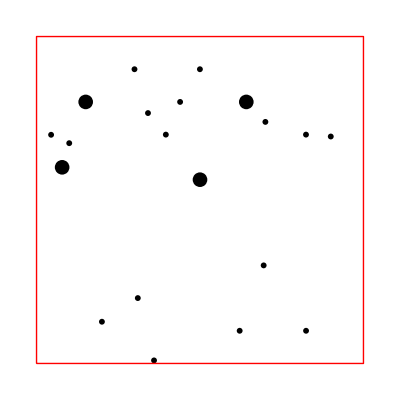

```mathematica
displayParticles[positions, radii, size]
```

```mathematica
cellA
```

<|7→{2,1},6→{8,1},9→{3,1},10→{10,1},2→{8,8},4→{1,8},5→{9,7},8→{7,8},1→{6,1},3→{6,1}|>

```mathematica
hash
```

<|1→1,2→9,3→5,4→8,5→4,6→6,7→3,8→10,9→2,10→7|>

```mathematica
heap
```

{{2.7522,1},{2.75449,9},{2.85303,7},{3.40177,5},{3.00089,3},{3.5913,6},{3.6903,10},{3.42459,4},{4.10687,2},{3.35638,8}}

```mathematica
ncollisions
```

671

```mathematica
nchecks
```

515